```mathematica
Quit[]
```

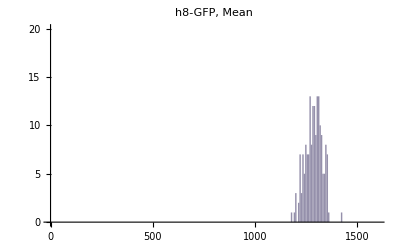

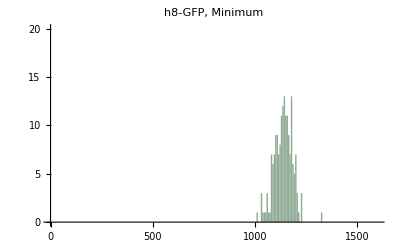

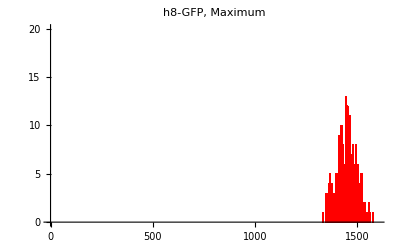

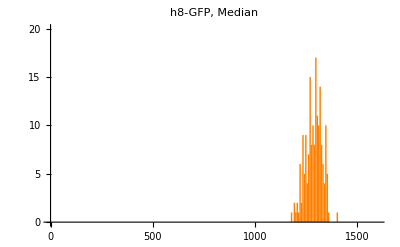

```mathematica
(* Specifying working directory and file name *)
workingDirectory = "D:\\labs\\toggle switch\\GfpRfpIntensities\\";
fileName = "h8-GFP.xlsx";

(* importing the file *)
xlData  = Import[workingDirectory<> fileName][[1]]; 
Data = ToExpression[ xlData[[2;;-2]]];
toPlot = Data[[All,3]];
histoBin = 7;

r = 25/256;
g = 188/256;
b = 157/256;
graph1 = Histogram[
Data[[All,3]],
{histoBin}, PlotRange->{{0,1600},{0,20}}, 
AxesOrigin->{0,0}, 
ChartStyle->{{RGBColor[r,g,b]} , EdgeForm[None]},
Ticks->{{0,500,1000,1500}, {0,5,10,15,20}}, 
PlotLabel->"h8-GFP, Mean"
]

r = 50/256;
g = 151/256;
b = 219/256;
graph2 = Histogram[
Data[[All,4]],
{histoBin}, PlotRange->{{0,1600},{0,20}}, 
AxesOrigin->{0,0}, 
ChartStyle->{{RGBColor[r,g,b]} , EdgeForm[None]},
Ticks->{{0,500,1000,1500}, {0,5,10,15,20}}, 
PlotLabel->"h8-GFP, Minimum"
]

r = 232/256;
g = 76/256;
b = 61/256;
graph3 = Histogram[
Data[[All,5]],
{histoBin}, PlotRange->{{0,1600},{0,20}}, 
AxesOrigin->{0,0}, 
ChartStyle->{{Red} , EdgeForm[None]},
Ticks->{{0,500,1000,1500}, {0,5,10,15,20}}, 
PlotLabel->"h8-GFP, Maximum"
]

r = 243/256;
g = 156/256;
b = 17/256;
graph4 = Histogram[
Data[[All,6]],
{histoBin}, PlotRange->{{0,1600},{0,20}}, 
AxesOrigin->{0,0}, 
ChartStyle->{{Orange} , EdgeForm[None]},
Ticks->{{0,500,1000,1500}, {0,5,10,15,20}}, 
PlotLabel->"h8-GFP, Median"
]
```

```mathematica
Show[{graph1,graph2,graph3,graph4}]
```